# Entanglement Distillation

See also Section 7.3 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Here, we start with a number of partially entangled pairs and “distills” a smaller number of maximally entangled pairs. This is illustrated in the quantum circuit model.

VonNeumannEntropy | VonNeumann entropy of a mixed state
PartialTrace | Partial trace over some subsystems
Dyad | Dyadic product of two vectors

Functions used in this document.

Make sure that Q3 is loaded.

```mathematica
<<Q3`
```

We have two parties Alice (A) and Bob (B). Teddy (T)  is an ancillary register to perform a measurement of the total Pauli Z.

```mathematica
Let[Qubit,A,B,T]
```

We will start with n partially entangled pairs.

```mathematica
$n=4;
kk=Range[$n];
AA=A[kk,$];
BB=B[kk,$];
```

You need fewer qubits for T, just enough to store a number up to maximum n.

```mathematica
ln=Ceiling@Log[2,$n+1];
TT=T[Range@ln,$];
```

## To Generate Partially Entangled Pairs

### A Single Pair

Let us first examine a single pair of partially entangled qubits.

First, construct a superposition of the two computational basis states  with different amplitudes.

```mathematica
Let[Real,ϕ]
qc=QuantumCircuit[
Ket[A@{1}],
Rotation[ϕ,A[1,2]]]
```

-Graphics-

Parameter ϕ tunes the two amplitudes, c_0=cos(ϕ/2) and c_1=sin(ϕ/2), in the superposition.

```mathematica
Elaborate[qc]//ExpandAll
```

Cos[ϕ/2] 0_A_1+1_A_1 Sin[ϕ/2]

Then, by applying the CNOT gate, you can create a partially entangled pair.

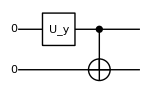

```mathematica
qc=QuantumCircuit[
Ket[{A[1],B[1]}],
Rotation[ϕ,A[1,2]],
CNOT[A[1],B[1]]]
```

Eventually, we see that the parameter ϕ tunes the extent of entanglement (with ϕ=π/2 corresponds to the maximal entanglement).

```mathematica
out=Elaborate[qc]
```

Cos[ϕ/2] 0_A_10_B_1+1_A_11_B_1 Sin[ϕ/2]

Examine the reduced density matrix for the first qubit to check that the above state is partial entangled.

```mathematica
rho=PartialTrace[out,B[1]]//ExpToTrig//Simplify;
Matrix[rho]//ExpToTrig//SimplifyThrough//MatrixForm
```

(Cos[ϕ/2]^2 | 0
0 | Sin[ϕ/2]^2)

### Multiple Pairs

Now, we consider n partially entangled pairs with each pair in the state described above. Let us take a look at the explicit expression for the n partially entangled pairs. Here, OTimes  is used just for better readability, and you can replace it with CircleTimes (⊗) or Multiply to get exactly the same result.

Repeating the above procedure for other pairs, generate as many partially entangled pairs as  you like. In this particular example, we prepare four pairs.

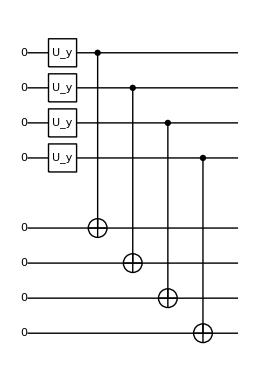

```mathematica
qc0=QuantumCircuit[
Ket[AA],Ket[BB],
Rotation[ϕ,A[kk,2]],
Sequence@@ReleaseHold@Thread@Hold[CNOT][AA,BB],
"Invisible"->A[$n+1/2]
]
```

Expanding it, one gets various terms, each with identical parts on Alice’s and Bob’s side.

```mathematica
out=Elaborate[qc0];
ProductForm[out,{AA,BB}]
```

Cos[ϕ/2]^4 0000⊗0000+Cos[ϕ/2]^3 0001⊗0001 Sin[ϕ/2]+1111⊗1111 Sin[ϕ/2]^4+1/2 Cos[ϕ/2]^2 0100⊗0100 Sin[ϕ]+1/2 Cos[ϕ/2]^2 1000⊗1000 Sin[ϕ]+1/2 0111⊗0111 Sin[ϕ/2]^2 Sin[ϕ]+1/2 1011⊗1011 Sin[ϕ/2]^2 Sin[ϕ]+1/2 1101⊗1101 Sin[ϕ/2]^2 Sin[ϕ]+1/2 1110⊗1110 Sin[ϕ/2]^2 Sin[ϕ]+1/4 Cot[ϕ/2] 0010⊗0010 Sin[ϕ]^2+1/4 0011⊗0011 Sin[ϕ]^2+1/4 0101⊗0101 Sin[ϕ]^2+1/4 0110⊗0110 Sin[ϕ]^2+1/4 1001⊗1001 Sin[ϕ]^2+1/4 1010⊗1010 Sin[ϕ]^2+1/4 1100⊗1100 Sin[ϕ]^2

If Alice (or Bob) measures the total Z, i.e., Z=Z_1+Z_2+…+Z_n on her qubits (see below), then the possible outcomes are  m=0,1,…,n and the corresponding probabilities are given by the following formula.

```mathematica
prb[ϕ_,m_]:=With[{p=Sin[ϕ/2]^2},Binomial[$n,m]*(1-p)^($n-m)p^m]
```

For fixed ϕ, the probability distribution looks like the following plot. The highest probability is for m=nsin^2(ϕ/2) (m=3 for ϕ=2π/3).

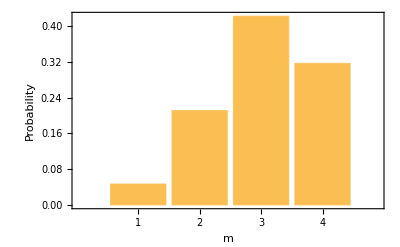

```mathematica
BarChart[
Table[prb[2Pi/3,m],{m,$n}],
ChartLabels->Range[$n],
Axes->None,Frame->True,
FrameLabel->{"m","Probability"}
]
```

## Measurement of Total Pauli Z

How can we actually measure Z_tot:=Z_1+Z_2+…+Z_non Bob's (or, equivalently, Alice's) qubits.

To specific, we assume ϕ=2π/3 from now on.

```mathematica
ϕ=2Pi/3
```

(2 π)/3

This is a tiny utility function for convenience.

```mathematica
bundle[]:=Flatten@Table[bundle[c],{c,$n}]
bundle[c_]:=With[
{log=Ceiling@Log[2,c+1]},
Table[
CNOT[Prepend[T@Range[k-1],B[c]],T[k]],
{k,log,1,-1}
]
]
```

The value of Z_tot is stored on Teddy's register.

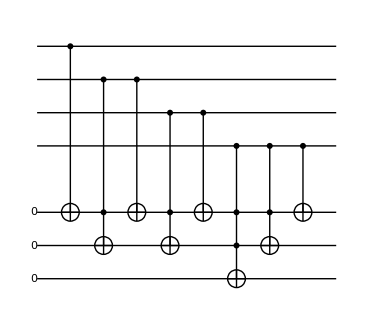

```mathematica
qc1=QuantumCircuit[
Ket[TT],
Sequence@@bundle[],
"Invisible"->B[$n+1/2]]
```

Let us check that the above quantum circuit indeed gives the sum of the bit values of the Bob’s qubits.

```mathematica
in=Basis[BB];
out=qc1**in;
```

```mathematica
sum=FromDigits[#,2]&/@Reverse/@Through[out[TT]];
Thread[SimpleForm[in]->sum]//TableForm
```

0000→0
0001→1
0010→1
0011→2
0100→1
0101→2
0110→2
0111→3
1000→1
1001→2
1010→2
1011→3
1100→2
1101→3
1110→3
1111→4

In actual situation, one must perform the measurement on Teddy's register in the computational basis. The measurement outcome refers to the value of Z_tot.

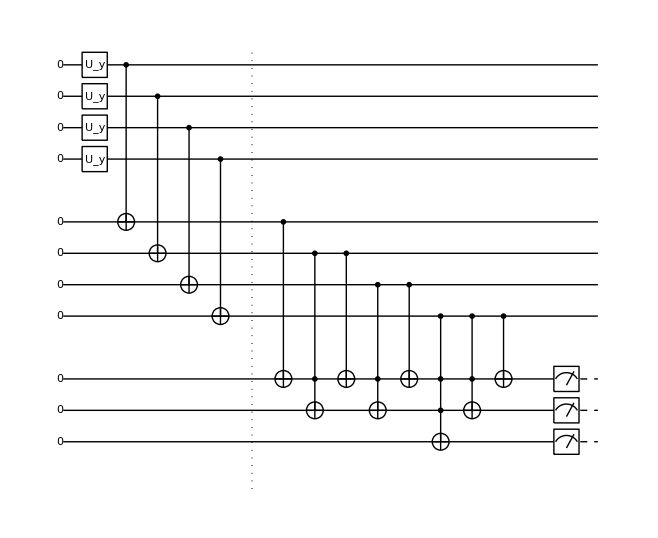

```mathematica
qc2=QuantumCircuit[
"Invisible"->{A[$n+1/2],B[$n+1/2],T[5]},
qc0,"Separator",qc1,"Spacer",Measurement[T[Range@ln,3]]]
```

## Transformation

The post-measurement state is spread over the four qubits of Alice's and Bob's registers, respectively. One has to transform it into a smaller number of pairs. Here, we assume that the measurement outcome is Z_tot=3, corresponding to two maximally entangled pairs. Note that  measurement outcome Z_tot=1also leads to two maximally entangled pairs since Binomial[4,1]==Binomial[4,3]==4.

To get the unitary transformation on Alice's side, we first rearrange the computational basis to get a new basis

𝒜:={0111,1011,1101,1110,α_5,…,α_16},

where α_k (k=5,…,16) are the computational basis states with total spin not equal to 3. Next, consider still another basis
	𝒜':={00;00,01;00,10;00,11;00,α'_5,…,α'_16},

where we have put a semicolon ';' to indicate the first two qubits to which encode Alice’s part of the maximally entangled states. Then, the required unitary transformation corresponds to the basis change from 𝒜 to 𝒜'. That is to say, the unitary transformation is given by

U:=00;000111+01;001011+10;001101+11;001110+Σ_(k=5)^16 a'_kα_k.

The unitary transformation on Bob's register may be obtained in the same manner, where we denote the rearranged bases by ℬ and ℬ'

### Method 1: Using Dyad

These are the computational bases for Alice's and Bob's registers, respectively.

```mathematica
bsA=Basis[AA]
bsB=Basis[BB]
```

{0_A_10_A_20_A_30_A_4,0_A_10_A_20_A_31_A_4,0_A_10_A_21_A_30_A_4,0_A_10_A_21_A_31_A_4,0_A_11_A_20_A_30_A_4,0_A_11_A_20_A_31_A_4,0_A_11_A_21_A_30_A_4,0_A_11_A_21_A_31_A_4,1_A_10_A_20_A_30_A_4,1_A_10_A_20_A_31_A_4,1_A_10_A_21_A_30_A_4,1_A_10_A_21_A_31_A_4,1_A_11_A_20_A_30_A_4,1_A_11_A_20_A_31_A_4,1_A_11_A_21_A_30_A_4,1_A_11_A_21_A_31_A_4}

{0_B_10_B_20_B_30_B_4,0_B_10_B_20_B_31_B_4,0_B_10_B_21_B_30_B_4,0_B_10_B_21_B_31_B_4,0_B_11_B_20_B_30_B_4,0_B_11_B_20_B_31_B_4,0_B_11_B_21_B_30_B_4,0_B_11_B_21_B_31_B_4,1_B_10_B_20_B_30_B_4,1_B_10_B_20_B_31_B_4,1_B_10_B_21_B_30_B_4,1_B_10_B_21_B_31_B_4,1_B_11_B_20_B_30_B_4,1_B_11_B_20_B_31_B_4,1_B_11_B_21_B_30_B_4,1_B_11_B_21_B_31_B_4}

These are the bases 𝒜 and ℬ for Alice's and Bob's registers, respectively.

```mathematica
bb=Permutations[PadLeft[Table[1,3],$n]];
sppA=Ket[AA->#]&/@bb;
sppB=Ket[BB->#]&/@bb;
sppA=Join[sppA,Sort@Complement[bsA,sppA]]
sppB=Join[sppB,Sort@Complement[bsB,sppB]]
```

{0_A_11_A_21_A_31_A_4,1_A_10_A_21_A_31_A_4,1_A_11_A_20_A_31_A_4,1_A_11_A_21_A_30_A_4,0_A_10_A_20_A_30_A_4,0_A_10_A_20_A_31_A_4,0_A_10_A_21_A_30_A_4,0_A_10_A_21_A_31_A_4,0_A_11_A_20_A_30_A_4,0_A_11_A_20_A_31_A_4,0_A_11_A_21_A_30_A_4,1_A_10_A_20_A_30_A_4,1_A_10_A_20_A_31_A_4,1_A_10_A_21_A_30_A_4,1_A_11_A_20_A_30_A_4,1_A_11_A_21_A_31_A_4}

{0_B_11_B_21_B_31_B_4,1_B_10_B_21_B_31_B_4,1_B_11_B_20_B_31_B_4,1_B_11_B_21_B_30_B_4,0_B_10_B_20_B_30_B_4,0_B_10_B_20_B_31_B_4,0_B_10_B_21_B_30_B_4,0_B_10_B_21_B_31_B_4,0_B_11_B_20_B_30_B_4,0_B_11_B_20_B_31_B_4,0_B_11_B_21_B_30_B_4,1_B_10_B_20_B_30_B_4,1_B_10_B_20_B_31_B_4,1_B_10_B_21_B_30_B_4,1_B_11_B_20_B_30_B_4,1_B_11_B_21_B_31_B_4}

These are the bases 𝒜' and ℬ' for Alice's and Bob's registers, respectively.

```mathematica
newA=Basis[A@{1,2}]//KetRegulate[#,AA]&;
newB=Basis[B@{1,2}]//KetRegulate[#,BB]&;
newA=Join[newA,Sort@Complement[bsA,newA]]
newB=Join[newB,Sort@Complement[bsB,newB]]
```

{0_A_10_A_20_A_30_A_4,0_A_11_A_20_A_30_A_4,1_A_10_A_20_A_30_A_4,1_A_11_A_20_A_30_A_4,0_A_10_A_20_A_31_A_4,0_A_10_A_21_A_30_A_4,0_A_10_A_21_A_31_A_4,0_A_11_A_20_A_31_A_4,0_A_11_A_21_A_30_A_4,0_A_11_A_21_A_31_A_4,1_A_10_A_20_A_31_A_4,1_A_10_A_21_A_30_A_4,1_A_10_A_21_A_31_A_4,1_A_11_A_20_A_31_A_4,1_A_11_A_21_A_30_A_4,1_A_11_A_21_A_31_A_4}

{0_B_10_B_20_B_30_B_4,0_B_11_B_20_B_30_B_4,1_B_10_B_20_B_30_B_4,1_B_11_B_20_B_30_B_4,0_B_10_B_20_B_31_B_4,0_B_10_B_21_B_30_B_4,0_B_10_B_21_B_31_B_4,0_B_11_B_20_B_31_B_4,0_B_11_B_21_B_30_B_4,0_B_11_B_21_B_31_B_4,1_B_10_B_20_B_31_B_4,1_B_10_B_21_B_30_B_4,1_B_10_B_21_B_31_B_4,1_B_11_B_20_B_31_B_4,1_B_11_B_21_B_30_B_4,1_B_11_B_21_B_31_B_4}

Finally, the unitary transformation is constructed as prescribed above.

```mathematica
trsA=Total@MapThread[Dyad[#1,#2,AA]&,{newA,sppA}]
trsB=Total@MapThread[Dyad[#1,#2,BB]&,{newB,sppB}]
```

0_A_10_A_20_A_30_A_40_A_11_A_21_A_31_A_4+0_A_10_A_20_A_31_A_40_A_10_A_20_A_30_A_4+0_A_10_A_21_A_30_A_40_A_10_A_20_A_31_A_4+0_A_10_A_21_A_31_A_40_A_10_A_21_A_30_A_4+0_A_11_A_20_A_30_A_41_A_10_A_21_A_31_A_4+0_A_11_A_20_A_31_A_40_A_10_A_21_A_31_A_4+0_A_11_A_21_A_30_A_40_A_11_A_20_A_30_A_4+0_A_11_A_21_A_31_A_40_A_11_A_20_A_31_A_4+1_A_10_A_20_A_30_A_41_A_11_A_20_A_31_A_4+1_A_10_A_20_A_31_A_40_A_11_A_21_A_30_A_4+1_A_10_A_21_A_30_A_41_A_10_A_20_A_30_A_4+1_A_10_A_21_A_31_A_41_A_10_A_20_A_31_A_4+1_A_11_A_20_A_30_A_41_A_11_A_21_A_30_A_4+1_A_11_A_20_A_31_A_41_A_10_A_21_A_30_A_4+1_A_11_A_21_A_30_A_41_A_11_A_20_A_30_A_4+1_A_11_A_21_A_31_A_41_A_11_A_21_A_31_A_4

0_B_10_B_20_B_30_B_40_B_11_B_21_B_31_B_4+0_B_10_B_20_B_31_B_40_B_10_B_20_B_30_B_4+0_B_10_B_21_B_30_B_40_B_10_B_20_B_31_B_4+0_B_10_B_21_B_31_B_40_B_10_B_21_B_30_B_4+0_B_11_B_20_B_30_B_41_B_10_B_21_B_31_B_4+0_B_11_B_20_B_31_B_40_B_10_B_21_B_31_B_4+0_B_11_B_21_B_30_B_40_B_11_B_20_B_30_B_4+0_B_11_B_21_B_31_B_40_B_11_B_20_B_31_B_4+1_B_10_B_20_B_30_B_41_B_11_B_20_B_31_B_4+1_B_10_B_20_B_31_B_40_B_11_B_21_B_30_B_4+1_B_10_B_21_B_30_B_41_B_10_B_20_B_30_B_4+1_B_10_B_21_B_31_B_41_B_10_B_20_B_31_B_4+1_B_11_B_20_B_30_B_41_B_11_B_21_B_30_B_4+1_B_11_B_20_B_31_B_41_B_10_B_21_B_30_B_4+1_B_11_B_21_B_30_B_41_B_11_B_20_B_30_B_4+1_B_11_B_21_B_31_B_41_B_11_B_21_B_31_B_4

By construction, the unitary transformations are just permutation, which is clear from their matrix representations.

```mathematica
Matrix[trsA]//MatrixForm
Matrix[trsB]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Check that they are indeed unitary transformations.

```mathematica
Dagger[trsA]**trsA//Elaborate
Dagger[trsB]**trsB//Elaborate
```

1

1

### Method 2: Using Permutation

Here, we find the permutation corresponding to the required basis change and use it to construct the unitary matrix.

```mathematica
conststructUnitary::usage="contructUnitary[m, n] finds the permutation of computational basis states of n qubits, where states with total spin m are mapped to the standard computational basis states of the first k qubits with other qubits set to zero. Here, k=Log[2,Binomial[n,m]]. It returns the matrix representing the permutation.";
```

```mathematica
constructUnitary::bad="States with `` non-zero qubits in a register of `` qubits cannot be encoded in a finite number of qubits.";
```

```mathematica
constructUnitary[m_Integer,n_Integer]:=Module[
{org=Tuples[{0,1},n],
bin=Log[2,Binomial[n,m]],
src,dst},
If[Not@IntegerQ@bin,
Message[constructUnitary::bad,m,n];
Return[One@Power[2,n]]
];
src=Permutations@PadLeft[Table[1,m],n];
src=DeleteDuplicates@Join[src,org];
dst=PadRight[#,n]&/@Tuples[{0,1},bin];
dst=DeleteDuplicates@Join[dst,org];
tau=FindPermutation[src,org];
tau=FindPermutation@Permute[dst,tau];
PermutationMatrix[tau,Power[2,n]]
]
```

Take an example for m=3. Each row or column contains exactly one element of value 1 and all other elements are zero, indicating the matrix represents a permutation.

```mathematica
mat=constructUnitary[3,4];
mat//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Construct the operators corresponding to the above matrix.

```mathematica
trsA=ExpressionFor[mat,AA]//Elaborate;
trsB=ExpressionFor[mat,BB]//Elaborate;
```

Examine if the operator properly maps the computational basis states for Alice's qubits.

```mathematica
in=Basis[AA];
out=trsA**in;
Thread[in->out]//TableForm
```

0_A_10_A_20_A_30_A_4→0_A_10_A_20_A_31_A_4
0_A_10_A_20_A_31_A_4→0_A_10_A_21_A_30_A_4
0_A_10_A_21_A_30_A_4→0_A_10_A_21_A_31_A_4
0_A_10_A_21_A_31_A_4→0_A_11_A_20_A_31_A_4
0_A_11_A_20_A_30_A_4→0_A_11_A_21_A_30_A_4
0_A_11_A_20_A_31_A_4→0_A_11_A_21_A_31_A_4
0_A_11_A_21_A_30_A_4→1_A_10_A_20_A_31_A_4
0_A_11_A_21_A_31_A_4→0_A_10_A_20_A_30_A_4
1_A_10_A_20_A_30_A_4→1_A_10_A_21_A_30_A_4
1_A_10_A_20_A_31_A_4→1_A_10_A_21_A_31_A_4
1_A_10_A_21_A_30_A_4→1_A_11_A_20_A_31_A_4
1_A_10_A_21_A_31_A_4→0_A_11_A_20_A_30_A_4
1_A_11_A_20_A_30_A_4→1_A_11_A_21_A_30_A_4
1_A_11_A_20_A_31_A_4→1_A_10_A_20_A_30_A_4
1_A_11_A_21_A_30_A_4→1_A_11_A_20_A_30_A_4
1_A_11_A_21_A_31_A_4→1_A_11_A_21_A_31_A_4

Also examine if the operator properly maps the computational basis states for Bob's qubits.

```mathematica
in=Basis[BB];
out=trsB**in;
Thread[in->out]//TableForm
```

0_B_10_B_20_B_30_B_4→0_B_10_B_20_B_31_B_4
0_B_10_B_20_B_31_B_4→0_B_10_B_21_B_30_B_4
0_B_10_B_21_B_30_B_4→0_B_10_B_21_B_31_B_4
0_B_10_B_21_B_31_B_4→0_B_11_B_20_B_31_B_4
0_B_11_B_20_B_30_B_4→0_B_11_B_21_B_30_B_4
0_B_11_B_20_B_31_B_4→0_B_11_B_21_B_31_B_4
0_B_11_B_21_B_30_B_4→1_B_10_B_20_B_31_B_4
0_B_11_B_21_B_31_B_4→0_B_10_B_20_B_30_B_4
1_B_10_B_20_B_30_B_4→1_B_10_B_21_B_30_B_4
1_B_10_B_20_B_31_B_4→1_B_10_B_21_B_31_B_4
1_B_10_B_21_B_30_B_4→1_B_11_B_20_B_31_B_4
1_B_10_B_21_B_31_B_4→0_B_11_B_20_B_30_B_4
1_B_11_B_20_B_30_B_4→1_B_11_B_21_B_30_B_4
1_B_11_B_20_B_31_B_4→1_B_10_B_20_B_30_B_4
1_B_11_B_21_B_30_B_4→1_B_11_B_20_B_30_B_4
1_B_11_B_21_B_31_B_4→1_B_11_B_21_B_31_B_4

## Overall

Now, we have all components. Our desired quantum circuit is as follows. The first part generates four partially entangled pairs, the second measures the total Pauli Z on Bob's register, and the last transforms the post-measurement state a fixed pair of qubits from Alice's and Bob's registers.

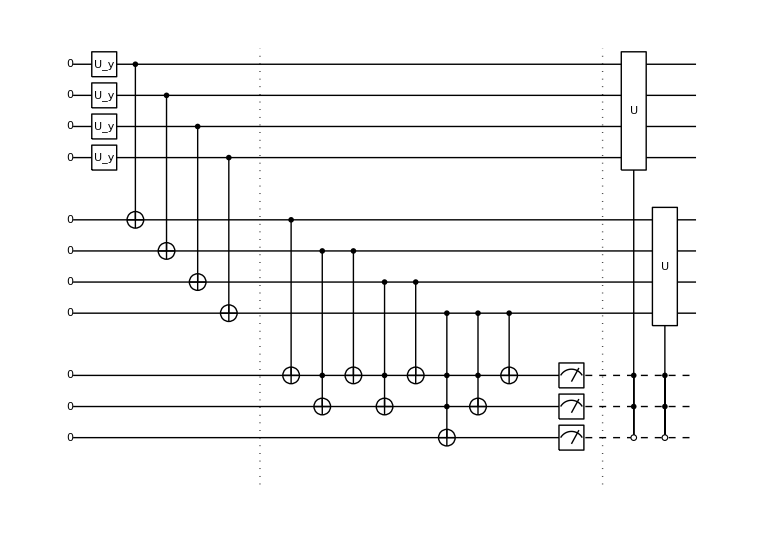

```mathematica
all=QuantumCircuit[qc2,"Separator",
ControlledGate[T@{1,2,3}->{1,1,0},trsA,"Label"->"U"],
ControlledGate[T@{1,2,3}->{1,1,0},trsB,"Label"->"U"],
]
```

Because the transformation on Alice’s and Bob’s sides are designed for the measurement outcome of Z_tot=3, we just run the quantum circuit until we get the desired outcome.

```mathematica
Until[ztot==3,
EchoTiming[out=Elaborate[all]];
ztot=FromDigits[Reverse@Readout[Through[TT[3]]],2];
PrintTemporary["Z_tot=",ztot]
];
```

0.528074

Here is the output state of the total system. Obviously, the whole register T is separated from the other two registers. So are the last two registers of the respective registers A and B.

```mathematica
out
```

1/2 0_A_10_A_20_A_30_A_40_B_10_B_20_B_30_B_41_T_11_T_20_T_3+1/2 0_A_11_A_20_A_30_A_40_B_11_B_20_B_30_B_41_T_11_T_20_T_3+1/2 1_A_10_A_20_A_30_A_41_B_10_B_20_B_30_B_41_T_11_T_20_T_3+1/2 1_A_11_A_20_A_30_A_41_B_11_B_20_B_30_B_41_T_11_T_20_T_3

Focusing on the first two qubits of registers A and B, we see that there are two maximally entangled pairs.

```mathematica
SimpleForm[out,{A@{1,2},B@{1,2}}]
```

(00;00)/2+(01;01)/2+(10;10)/2+(11;11)/2

```mathematica
KetFactor@KetDrop[out,TT]
```

1/2 0_A_30_A_4⊗(0_A_10_B_1+1_A_11_B_1)⊗(0_A_20_B_2+1_A_21_B_2)⊗0_B_30_B_4

### Remark

So, we have successfully generated two maximally entangled pairs from four partially entangled pairs. Note that this was possible because we assumed that the measurement outcome was m=3. The case with m=1 is also handled following a similar procedure.

However, if the measurement outcome is m=2, resulting in the post-measurement state

1/6 0011⊗0011+1/6 0101⊗0101+1/6 0110⊗0110+1/6 1001⊗1001+1/6 1010⊗1010+1/6 1100⊗1100

then there is no way to turn this state into a product state on a system of qubits.

Related Guides

Quantum Information Systems

Quantum Many-Body Systems

Quantum Spin Systems

Related Tech Notes

A Quantum Playbook

Entanglement Distillation

Quantum Information Theory

Quantum Information Systems with Q3

Quantum Many-Body Systems with Q3

Quantum Spin Systems with Q3

Related Links

J. Preskill (1998), Lecture Notes for Physics 229: Quantum Information and Computation.

M. Nielsen and I. L. Chuang (2022), Quantum Computation and Quantum Information (Cambridge University Press, 2011).

Mahn-Soo Choi (2022), A Quantum Computation Workbook (Springer, 2022).

## Metadata

### Categorization

Tech Note

QuantumPlaybook

QuantumPlaybook`

QuantumPlaybook/tutorial/EntanglementDistillation

### Keywords

quantum entanglement

entanglement distillation

entanglement purification